```mathematica
$Assumptions={h>0,h<a,a>0,airDensity>0,waterDensity>0,waterDensity>airDensity}
```

{h>0,h<a,a>0,airDensity>0,waterDensity>0,waterDensity>airDensity}

```mathematica
ρ[x_]=Piecewise[{{waterDensity,x<h},{airDensity,True}}]
CG=Integrate[x*ρ[x],{x,0,a}]/Integrate[ρ[x],{x,0,a}]
```

Piecewise[{{waterDensity, x<h}, {airDensity, True}}]

(a^2 airDensity-airDensity h^2+h^2 waterDensity)/(2 (a airDensity-airDensity h+h waterDensity))

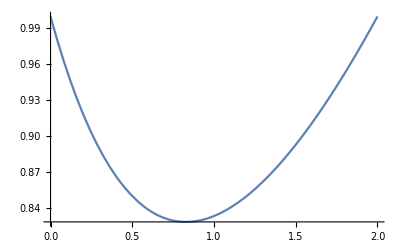

```mathematica
Plot[CG/.{a->2, airDensity->1,waterDensity->2},{h,0,2}]
```

```mathematica
D[CG,h]==0
```

(-2 airDensity h+2 h waterDensity)/(2 (a airDensity-airDensity h+h waterDensity))-((-airDensity+waterDensity) (a^2 airDensity-airDensity h^2+h^2 waterDensity))/(2 (a airDensity-airDensity h+h waterDensity)^2)==0

```mathematica
findZero=Evaluate[D[CG,h]]//Simplify
```

((a^2 airDensity-2 a airDensity h+h^2 (airDensity-waterDensity)) (airDensity-waterDensity))/(2 (a airDensity+h (-airDensity+waterDensity))^2)

```mathematica
Normal[Solve[findZero==0,h]]//Simplify
```

{{h→(a (airDensity-√(airDensity waterDensity)))/(airDensity-waterDensity)}}